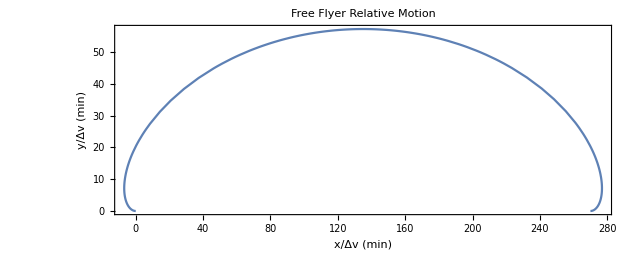

```mathematica
(* Case 1 *)

ω=(2 π)/90; (* 1/min *)
T=90; (* min *)
x[t_]:=-4/ω Sin[ω t]+3 t
y[t_]:=2/ω(1-Cos[ω t])
ParametricPlot[{x[t],y[t]},{t,0,T},Frame->{True,True},FrameLabel->{"x/Δv (min)","y/Δv (min)"},PlotLabel-> Style["Free Flyer Relative Motion",14]]
```

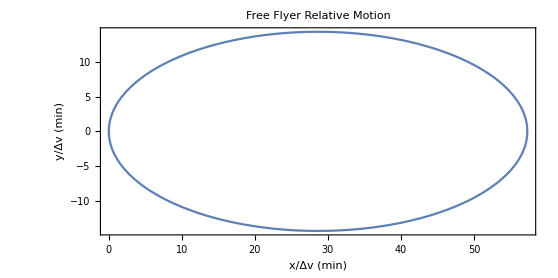

```mathematica
(* Case 2 *)

ω=(2 π)/90; (* 1/min *)
T=90; (* min *)
x[t_]:=2/ω(1-Cos[ω t])
y[t_]:=1/ω Sin[ω t]
ParametricPlot[{x[t],y[t]},{t,0,T},Frame->{True,True},FrameLabel->{"x/Δv (min)","y/Δv (min)"},PlotLabel-> Style["Free Flyer Relative Motion",14]]
```